```mathematica
(*Loading the melt package*)
Get["http://www.fmt.if.usp.br/~gtlandi/download/melt.m"]
LoadPauliMatrices[];
SetOptions[Plot,BaseStyle->{FontFamily->"Times New Roman",FontSize->15}];
```

## Figure 2.4a

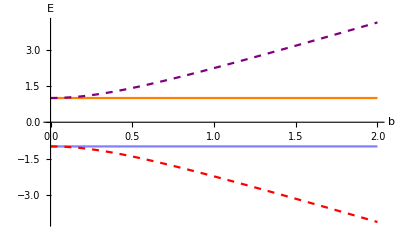

```mathematica
(*Compute eigenspectrum for Ising Hamiltonian*)
Δ=0.;
hamis= kron[σx,σx]+Δ*kron[σz,σz]-b (KronEye[σz,2,1]+KronEye[σz,2,2]);
eigsis=Eigvals[hamis];
is2spectra=Plot[{eigsis[[1]],eigsis[[2]],eigsis[[3]],eigsis[[4]]},{b,0,2},LabelStyle->Directive[Black,15],AxesLabel->{"b","E"},PlotStyle->{{Blue,Opacity[0.5]},{Orange},{Red,Dashed},{Purple,Dashed}}]
```

```mathematica
Export[SystemDialogInput["FileSave", "n2_ising_energies.png"],is2spectra,Background->None];
```

## Figure 2.4b

```mathematica
rzy[θ_]:=Cos[θ]*σz+Sin[θ]*σy 
J=5.;
```

### n = 2

```mathematica
B//Clear
β//Clear
vals2={};
Dynamic[j]
do[B=j;ham2 = -J*(kron[σx,σx])+B*(kron[σz,σ0]+kron[σ0,σz]);gsGHZ=Eigenvectors[ham2][[1]];ρ2=out[gsGHZ,gsGHZ];(rot2=kron[rzy[θ],rzy[ϕ]]//Simplify);(corr2[θ_,ϕ_]=Tr[rot2.ρ2]//Simplify);
Svet2=1/2 (corr2[θ1, ϕ1]+corr2[θ2, ϕ1]+corr2[θ1, ϕ2]-corr2[θ2, ϕ2]);sval=NMaximize[Svet2,{θ1,θ2,ϕ1,ϕ2}][[1]];AppendTo[vals2,{j,sval}],{j,0.5,20,0.5}]
vals2
```

0h : 0m : 1s

### n = 3

```mathematica
B//Clear
β//Clear
vals3={};
Dynamic[j]
do[B=j;ham3 = -J*(kron[σx,σx,σ0]+kron[σ0,σx,σx]+kron[σx,σ0,σx])+B*(kron[σz,σ0,σ0]+kron[σ0,σz,σ0]+kron[σ0,σ0,σz]);gsGHZ=Eigenvectors[ham3][[1]];ρ3=out[gsGHZ,gsGHZ];(rot3=kron[rzy[θ],rzy[ϕ],rzy[φ]]//Simplify);(corr3[θ_,ϕ_,φ_]=Tr[rot3.ρ3]//Simplify);
Svet3=1/4 (-corr3[θ1,ϕ1,φ1]+corr3[θ2, ϕ1, φ1]+corr3[θ1, φ1, ϕ2]+corr3[θ2, φ1, ϕ2]+corr3[θ1, ϕ1, φ2]+corr3[θ2, ϕ1, φ2]+corr3[θ1, ϕ2, φ2]-corr3[θ2, ϕ2, φ2]);sval=NMaximize[Svet3,{θ1,θ2,ϕ1,ϕ2,φ1,φ2}][[1]];AppendTo[vals3,{j,sval}],{j,0.5,20,0.5}]
vals3
```

0h : 0m : 2s

{{0.5,1.41129},{1.,1.40149},{1.5,1.38345},{2.,1.35643},{2.5,1.32069},{3.,1.27769},{3.5,1.22992},{4.,1.18046},{4.5,1.13243},{5.,1.08866},{5.5,1.0515},{6.,1.02295},{6.5,1.00502},{7.,1.},{7.5,1.},{8.,1.},{8.5,1.},{9.,1.},{9.5,1.},{10.,1.},{10.5,1.},{11.,1.},{11.5,1.},{12.,1.},{12.5,1.},{13.,1.},{13.5,1.},{14.,1.},{14.5,1.},{15.,1.},{15.5,1.},{16.,1.},{16.5,1.},{17.,1.},{17.5,1.},{18.,1.},{18.5,1.},{19.,1.},{19.5,1.},{20.,1.}}

### n = 4

```mathematica
B//Clear
β//Clear
vals4={};
Dynamic[j]
do[B=j;ham4 = -J*(kron[σx,σx,σ0,σ0]+kron[σ0,σx,σx,σ0]+kron[σ0,σ0,σx,σx]+kron[σx,σ0,σ0,σx])+B*(kron[σz,σ0,σ0,σ0]+kron[σ0,σz,σ0,σ0]+kron[σ0,σ0,σz,σ0]+kron[σ0,σ0,σ0,σz]);gsGHZ=Eigenvectors[ham4][[1]];ρ4=out[gsGHZ,gsGHZ];(rot4=kron[rzy[θ],rzy[ϕ],rzy[φ],rzy[ψ]]//Simplify);(corr4[θ_,ϕ_,φ_,ψ_]=Tr[rot4.ρ4]//Simplify);
Svet4=1/4 (-corr4[θ1, ϕ1, φ1, ψ1]+corr4[θ2, ϕ1, φ1, ψ1]+corr4[θ1, φ1, ϕ2, ψ1]+corr4[θ2, φ1, ϕ2, ψ1]+corr4[θ1, ϕ1, φ2, ψ1]+corr4[θ2, ϕ1, φ2, ψ1]+corr4[θ1, ϕ2, φ2, ψ1]-corr4[θ2, ϕ2, φ2, ψ1]+corr4[θ1, ϕ1, φ1, ψ2]+corr4[θ2, ϕ1, φ1, ψ2]+corr4[θ1, φ1, ϕ2, ψ2]-corr4[θ2, φ1, ϕ2, ψ2]+corr4[θ1, ϕ1, φ2, ψ2]-corr4[θ2, ϕ1, φ2, ψ2]-corr4[θ1, ϕ2, φ2, ψ2]-corr4[θ2, ϕ2, φ2, ψ2]);sval=NMaximize[Svet4,{θ1,θ2,ϕ1,ϕ2,φ1,φ2,ψ1,ψ2}][[1]];AppendTo[vals4,{j,sval}],{j,0.5,20,0.5}]
vals4
```

0h : 0m : 7s

{{0.5,2.82128},{1.,2.79899},{1.5,2.75914},{2.,2.6983},{2.5,2.61323},{3.,2.50259},{3.5,2.36875},{4.,2.21845},{4.5,2.06152},{5.,1.9081},{5.5,1.7662},{6.,1.64059},{6.5,1.53299},{7.,1.44305},{7.5,1.36913},{8.,1.30909},{8.5,1.2606},{9.,1.22152},{9.5,1.18993},{10.,1.16426},{10.5,1.14325},{11.,1.1259},{11.5,1.11146},{12.,1.09934},{12.5,1.08907},{13.,1.08031},{13.5,1.07277},{14.,1.06625},{14.5,1.06057},{15.,1.05975},{15.5,1.05121},{16.,1.05078},{16.5,1.04386},{17.,1.04077},{17.5,1.038},{18.,1.03551},{18.5,1.03325},{19.,1.0312},{19.5,1.02934},{20.,1.02764}}

### n = 5

```mathematica
B//Clear
β//Clear
vals5={};
Dynamic[j]
do[B=j;ham5 = -J*(kron[σx,σx,σ0,σ0,σ0]+kron[σ0,σx,σx,σ0,σ0]+kron[σ0,σ0,σx,σx,σ0]+kron[σ0,σ0,σ0,σx,σx]+kron[σx,σ0,σ0,σ0,σx])+B*(kron[σz,σ0,σ0,σ0,σ0]+kron[σ0,σz,σ0,σ0,σ0]+kron[σ0,σ0,σz,σ0,σ0]+kron[σ0,σ0,σ0,σz,σ0]+kron[σ0,σ0,σ0,σ0,σz]);gsGHZ=Eigenvectors[ham5][[1]];ρ5=out[gsGHZ,gsGHZ];(rot5=kron[rzy[θ],rzy[ϕ],rzy[φ],rzy[ψ],rzy[ω]]//Simplify);(corr5[θ_,ϕ_,φ_,ψ_,ω_]=Tr[rot5.ρ5]//Simplify);
Svet5=1/8(-corr5[θ1,ϕ1,φ1,ψ1,ω1]-corr5[θ2,ϕ1,φ1,ψ1,ω1]-corr5[θ1,φ1,ϕ2,ψ1,ω1]+corr5[θ2,φ1,ϕ2,ψ1,ω1]-corr5[θ1,ϕ1,φ2,ψ1,ω1]+corr5[θ2,ϕ1,φ2,ψ1,ω1]+corr5[θ1,ϕ2,φ2,ψ1,ω1]+corr5[θ2,ϕ2,φ2,ψ1,ω1]-corr5[θ1,ϕ1,φ1,ψ2,ω1]+corr5[θ2,ϕ1,φ1,ψ2,ω1]+corr5[θ1,φ1,ϕ2,ψ2,ω1]+corr5[θ2,φ1,ϕ2,ψ2,ω1]+corr5[θ1,ϕ1,φ2,ψ2,ω1]+corr5[θ2,ϕ1,φ2,ψ2,ω1]+corr5[θ1,ϕ2,φ2,ψ2,ω1]-corr5[θ2,ϕ2,φ2,ψ2,ω1]-corr5[θ1,ϕ1,φ1,ψ1,ω2]+corr5[θ2,ϕ1,φ1,ψ1,ω2]+corr5[θ1,φ1,ϕ2,ψ1,ω2]+corr5[θ2,φ1,ϕ2,ψ1,ω2]+corr5[θ1,ϕ1,φ2,ψ1,ω2]+corr5[θ2,ϕ1,φ2,ψ1,ω2]+corr5[θ1,ϕ2,φ2,ψ1,ω2]-corr5[θ2,ϕ2,φ2,ψ1,ω2]+corr5[θ1,ϕ1,φ1,ψ2,ω2]+corr5[θ2,ϕ1,φ1,ψ2,ω2]+corr5[θ1,φ1,ϕ2,ψ2,ω2]-corr5[θ2,φ1,ϕ2,ψ2,ω2]+corr5[θ1,ϕ1,φ2,ψ2,ω2]-corr5[θ2,ϕ1,φ2,ψ2,ω2]-corr5[θ1,ϕ2,φ2,ψ2,ω2]-corr5[θ2,ϕ2,φ2,ψ2,ω2]);sval=NMaximize[Svet5,{θ1,θ2,ϕ1,ϕ2,φ1,φ2,ψ1,ψ2,ω1,ω2}][[1]];AppendTo[vals5,{j,sval}],{j,0.5,20,0.5}]
vals5
```

0h : 0m : 27s

{{0.5,2.81957},{1.,2.79271},{1.5,2.74653},{2.,2.67814},{2.5,2.58317},{3.,2.45568},{3.5,2.29814},{4.,2.11119},{4.5,1.90893},{5.,1.70889},{5.5,1.52712},{6.,1.37076},{6.5,1.24491},{7.,1.14983},{7.5,1.07929},{8.,1.0301},{8.5,1.00612},{9.,1.},{9.5,1.},{10.,1.},{10.5,1.},{11.,1.},{11.5,1.},{12.,1.},{12.5,1.},{13.,1.},{13.5,1.},{14.,1.},{14.5,1.},{15.,1.},{15.5,1.},{16.,1.},{16.5,1.},{17.,1.},{17.5,1.},{18.,1.},{18.5,1.},{19.,1.},{19.5,1.},{20.,1.}}

### n = 6

```mathematica
B//Clear
β//Clear
vals6={};
Dynamic[j]
do[B=j;ham6 = -J*(kron[σx,σx,σ0,σ0,σ0,σ0]+kron[σ0,σx,σx,σ0,σ0,σ0]+kron[σ0,σ0,σx,σx,σ0,σ0]+kron[σ0,σ0,σ0,σx,σx,σ0]+kron[σ0,σ0,σ0,σ0,σx,σx]+kron[σx,σ0,σ0,σ0,σ0,σx])+B*(kron[σz,σ0,σ0,σ0,σ0,σ0]+kron[σ0,σz,σ0,σ0,σ0,σ0]+kron[σ0,σ0,σz,σ0,σ0,σ0]+kron[σ0,σ0,σ0,σz,σ0,σ0]+kron[σ0,σ0,σ0,σ0,σz,σ0]+kron[σ0,σ0,σ0,σ0,σ0,σz]);gsGHZ=Eigenvectors[ham6][[1]];ρ6=out[gsGHZ,gsGHZ];(rot6=kron[rzy[θ],rzy[ϕ],rzy[φ],rzy[ψ],rzy[ω],rzy[γ]]//Simplify);corr6[θ_,ϕ_,φ_,ψ_,ω_,γ_]=Tr[rot6.ρ6];
Svet6=1/8 (-corr6[γ1, θ1, ϕ1, φ1, ψ1, ω1]-corr6[γ2, θ1, ϕ1, φ1, ψ1, ω1]-corr6[γ1 ,θ2, ϕ1, φ1, ψ1, ω1]+corr6[γ2, θ2, ϕ1, φ1, ψ1, ω1]-corr6[γ1, θ1, φ1, ϕ2, ψ1, ω1]+corr6[γ2, θ1, φ1, ϕ2, ψ1, ω1]+corr6[γ1, θ2, φ1, ϕ2, ψ1, ω1]+corr6[γ2, θ2, φ1, ϕ2, ψ1, ω1]-corr6[γ1, θ1, ϕ1, φ2, ψ1, ω1]+corr6[γ2, θ1, ϕ1, φ2, ψ1, ω1]+corr6[γ1, θ2, ϕ1 ,φ2 ,ψ1, ω1]+corr6[γ2, θ2, ϕ1, φ2, ψ1, ω1]+corr6[γ1, θ1, ϕ2, φ2, ψ1, ω1]+corr6[γ2, θ1, ϕ2, φ2, ψ1, ω1]+corr6[γ1,θ2 ,ϕ2 ,φ2 ,ψ1 ,ω1]-corr6[γ2, θ2, ϕ2, φ2, ψ1, ω1]-corr6[γ1, θ1, ϕ1, φ1, ψ2, ω1]+corr6[γ2, θ1, ϕ1, φ1, ψ2, ω1]+corr6[γ1, θ2, ϕ1, φ1, ψ2, ω1]+corr6[γ2, θ2, ϕ1, φ1, ψ2, ω1]+corr6[γ1, θ1, φ1, ϕ2, ψ2, ω1]+corr6[γ2, θ1, φ1, ϕ2, ψ2, ω1]+corr6[γ1, θ2, φ1, ϕ2, ψ2, ω1]-corr6[γ2, θ2, φ1, ϕ2, ψ2, ω1]+corr6[γ1, θ1, ϕ1, φ2, ψ2, ω1]+corr6[γ2, θ1, ϕ1, φ2, ψ2, ω1]+corr6[γ1, θ2, ϕ1, φ2, ψ2, ω1]-corr6[γ2, θ2, ϕ1, φ2, ψ2, ω1]+corr6[γ1, θ1, ϕ2, φ2, ψ2, ω1]-corr6[γ2, θ1, ϕ2, φ2, ψ2, ω1]-corr6[γ1, θ2, ϕ2, φ2, ψ2, ω1]-corr6[γ2, θ2, ϕ2, φ2, ψ2, ω1]-corr6[γ1, θ1, ϕ1, φ1, ψ1, ω2]+corr6[γ2, θ1, ϕ1, φ1, ψ1, ω2]+corr6[γ1, θ2, ϕ1, φ1, ψ1, ω2]+corr6[γ2, θ2, ϕ1, φ1, ψ1, ω2]+corr6[γ1, θ1, φ1, ϕ2, ψ1, ω2]+corr6[γ2, θ1, φ1, ϕ2, ψ1, ω2]+corr6[γ1, θ2, φ1, ϕ2, ψ1, ω2]-corr6[γ2, θ2, φ1, ϕ2, ψ1, ω2]+corr6[γ1, θ1, ϕ1, φ2, ψ1, ω2]+corr6[γ2, θ1, ϕ1, φ2, ψ1, ω2]+corr6[γ1, θ2, ϕ1, φ2, ψ1, ω2]-corr6[γ2, θ2, ϕ1, φ2, ψ1, ω2]+corr6[γ1, θ1, ϕ2, φ2, ψ1, ω2]-corr6[γ2, θ1, ϕ2, φ2, ψ1, ω2]-corr6[γ1, θ2, ϕ2, φ2, ψ1, ω2]-corr6[γ2, θ2, ϕ2, φ2, ψ1, ω2]+corr6[γ1, θ1, ϕ1, φ1, ψ2, ω2]+corr6[γ2, θ1, ϕ1, φ1, ψ2, ω2]+corr6[γ1, θ2, ϕ1, φ1, ψ2, ω2]-corr6[γ2, θ2, ϕ1, φ1, ψ2, ω2]+corr6[γ1, θ1, φ1, ϕ2, ψ2, ω2]-corr6[γ2, θ1, φ1, ϕ2, ψ2, ω2]-corr6[γ1, θ2, φ1, ϕ2, ψ2, ω2]-corr6[γ2, θ2, φ1, ϕ2, ψ2, ω2]+corr6[γ1, θ1, ϕ1, φ2, ψ2, ω2]-corr6[γ2, θ1, ϕ1, φ2, ψ2, ω2]-corr6[γ1, θ2, ϕ1, φ2, ψ2, ω2]-corr6[γ2, θ2, ϕ1, φ2, ψ2, ω2]-corr6[γ1, θ1, ϕ2, φ2, ψ2, ω2]-corr6[γ2, θ1, ϕ2, φ2, ψ2, ω2]-corr6[γ1, θ2, ϕ2, φ2, ψ2, ω2]+corr6[γ2 ,θ2, ϕ2, φ2, ψ2 ,ω2]);sval=NMaximize[Svet6,{θ1,θ2,ϕ1,ϕ2,φ1,φ2,ψ1,ψ2,ω1,ω2,γ1,γ2}][[1]];AppendTo[vals6,{j,sval}],{j,0.5,20,0.5}]
vals6
```

0h : 3m : 46s

{{0.5,5.63563+0. ⅈ},{1.,5.57168+0. ⅈ},{1.5,5.46368+0. ⅈ},{2.,5.30781+0. ⅈ},{2.5,5.09622+0. ⅈ},{3.,4.81712+0. ⅈ},{3.5,4.45941+0. ⅈ},{4.,4.0243+0. ⅈ},{4.5,3.53766+0. ⅈ},{5.,3.04838+0. ⅈ},{5.5,2.60235+0. ⅈ},{6.,2.23222+0. ⅈ},{6.5,1.94045+0. ⅈ},{7.,1.71804+0. ⅈ},{7.5,1.5517+0. ⅈ},{8.,1.42865+0. ⅈ},{8.5,1.33807+0. ⅈ},{9.,1.27132+0. ⅈ},{9.5,1.22174+0. ⅈ},{10.,1.18438+0. ⅈ},{10.5,1.15575+0. ⅈ},{11.,1.13339+0. ⅈ},{11.5,1.11563+0. ⅈ},{12.,1.10128+0. ⅈ},{12.5,1.08952+0. ⅈ},{13.,1.07975+0. ⅈ},{13.5,1.07155+0. ⅈ},{14.,1.06458+0. ⅈ},{14.5,1.05861+0. ⅈ},{15.,1.05346+0. ⅈ},{15.5,1.04898+0. ⅈ},{16.,1.04505+0. ⅈ},{16.5,1.04158+0. ⅈ},{17.,1.03851+0. ⅈ},{17.5,1.03578+0. ⅈ},{18.,1.03333+0. ⅈ},{18.5,1.03113+0. ⅈ},{19.,1.02915+0. ⅈ},{19.5,1.02735+0. ⅈ},{20.,1.02572+0. ⅈ}}

### n = 7

```mathematica
B//Clear
β//Clear
vals7={};
Dynamic[j]
do[B=j;ham7 = -J*(kron[σx,σx,σ0,σ0,σ0,σ0,σ0]+kron[σ0,σx,σx,σ0,σ0,σ0,σ0]+kron[σ0,σ0,σx,σx,σ0,σ0,σ0]+kron[σ0,σ0,σ0,σx,σx,σ0,σ0]+kron[σ0,σ0,σ0,σ0,σx,σx,σ0]+kron[σ0,σ0,σ0,σ0,σ0,σx,σx]+kron[σx,σ0,σ0,σ0,σ0,σ0,σx])+B*(kron[σz,σ0,σ0,σ0,σ0,σ0,σ0]+kron[σ0,σz,σ0,σ0,σ0,σ0,σ0]+kron[σ0,σ0,σz,σ0,σ0,σ0,σ0]+kron[σ0,σ0,σ0,σz,σ0,σ0,σ0]+kron[σ0,σ0,σ0,σ0,σz,σ0,σ0]+kron[σ0,σ0,σ0,σ0,σ0,σz,σ0]+kron[σ0,σ0,σ0,σ0,σ0,σ0,σz]);gsGHZ=Eigenvectors[ham7][[1]];ρ7=out[gsGHZ,gsGHZ];(rot7=kron[rzy[θ],rzy[ϕ],rzy[φ],rzy[ψ],rzy[ω],rzy[γ],rzy[λ]]//Simplify);corr7[θ_,ϕ_,φ_,ψ_,ω_,γ_,λ_]=Tr[rot7.ρ7];
Svet7=1/16 (corr7[γ1,θ1,λ1,ϕ1,φ1,ψ1,ω1]-corr7[γ2,θ1,λ1,ϕ1,φ1,ψ1,ω1]-corr7[γ1,θ2,λ1,ϕ1,φ1,ψ1,ω1]-corr7[γ2,θ2,λ1,ϕ1,φ1,ψ1,ω1]-corr7[γ1,θ1,λ2,ϕ1,φ1,ψ1,ω1]-corr7[γ2,θ1,λ2,ϕ1,φ1,ψ1,ω1]-corr7[γ1,θ2,λ2,ϕ1,φ1,ψ1,ω1]+corr7[γ2,θ2,λ2,ϕ1,φ1,ψ1,ω1]-corr7[γ1,θ1,λ1,φ1,ϕ2,ψ1,ω1]-corr7[γ2,θ1,λ1,φ1,ϕ2,ψ1,ω1]-corr7[γ1,θ2,λ1,φ1,ϕ2,ψ1,ω1]+corr7[γ2,θ2,λ1,φ1,ϕ2,ψ1,ω1]-corr7[γ1,θ1,λ2,φ1,ϕ2,ψ1,ω1]+corr7[γ2,θ1,λ2,φ1,ϕ2,ψ1,ω1]+corr7[γ1,θ2,λ2,φ1,ϕ2,ψ1,ω1]+corr7[γ2,θ2,λ2,φ1,ϕ2,ψ1,ω1]-corr7[γ1,θ1,λ1,ϕ1,φ2,ψ1,ω1]-corr7[γ2,θ1,λ1,ϕ1,φ2,ψ1,ω1]-corr7[γ1,θ2,λ1,ϕ1,φ2,ψ1,ω1]+corr7[γ2,θ2,λ1,ϕ1,φ2,ψ1,ω1]-corr7[γ1,θ1,λ2,ϕ1,φ2,ψ1,ω1]+corr7[γ2,θ1,λ2,ϕ1,φ2,ψ1,ω1]+corr7[γ1,θ2,λ2,ϕ1,φ2,ψ1,ω1]+corr7[γ2,θ2,λ2,ϕ1,φ2,ψ1,ω1]-corr7[γ1,θ1,λ1,ϕ2,φ2,ψ1,ω1]+corr7[γ2,θ1,λ1,ϕ2,φ2,ψ1,ω1]+corr7[γ1,θ2,λ1,ϕ2,φ2,ψ1,ω1]+corr7[γ2,θ2,λ1,ϕ2,φ2,ψ1,ω1]+corr7[γ1,θ1,λ2,ϕ2,φ2,ψ1,ω1]+corr7[γ2,θ1,λ2,ϕ2,φ2,ψ1,ω1]+corr7[γ1,θ2,λ2,ϕ2,φ2,ψ1,ω1]-corr7[γ2,θ2,λ2,ϕ2,φ2,ψ1,ω1]-corr7[γ1,θ1,λ1,ϕ1,φ1,ψ2,ω1]-corr7[γ2,θ1,λ1,ϕ1,φ1,ψ2,ω1]-corr7[γ1,θ2,λ1,ϕ1,φ1,ψ2,ω1]+corr7[γ2,θ2,λ1,ϕ1,φ1,ψ2,ω1]-corr7[γ1,θ1,λ2,ϕ1,φ1,ψ2,ω1]+corr7[γ2,θ1,λ2,ϕ1,φ1,ψ2,ω1]+corr7[γ1,θ2,λ2,ϕ1,φ1,ψ2,ω1]+corr7[γ2,θ2,λ2,ϕ1,φ1,ψ2,ω1]-corr7[γ1,θ1,λ1,φ1,ϕ2,ψ2,ω1]+corr7[γ2,θ1,λ1,φ1,ϕ2,ψ2,ω1]+corr7[γ1,θ2,λ1,φ1,ϕ2,ψ2,ω1]+corr7[γ2,θ2,λ1,φ1,ϕ2,ψ2,ω1]+corr7[γ1,θ1,λ2,φ1,ϕ2,ψ2,ω1]+corr7[γ2,θ1,λ2,φ1,ϕ2,ψ2,ω1]+corr7[γ1,θ2,λ2,φ1,ϕ2,ψ2,ω1]-corr7[γ2,θ2,λ2,φ1,ϕ2,ψ2,ω1]-corr7[γ1,θ1,λ1,ϕ1,φ2,ψ2,ω1]+corr7[γ2,θ1,λ1,ϕ1,φ2,ψ2,ω1]+corr7[γ1,θ2,λ1,ϕ1,φ2,ψ2,ω1]+corr7[γ2,θ2,λ1,ϕ1,φ2,ψ2,ω1]+corr7[γ1,θ1,λ2,ϕ1,φ2,ψ2,ω1]+corr7[γ2,θ1,λ2,ϕ1,φ2,ψ2,ω1]+corr7[γ1,θ2,λ2,ϕ1,φ2,ψ2,ω1]-corr7[γ2,θ2,λ2,ϕ1,φ2,ψ2,ω1]+corr7[γ1,θ1,λ1,ϕ2,φ2,ψ2,ω1]+corr7[γ2,θ1,λ1,ϕ2,φ2,ψ2,ω1]+corr7[γ1,θ2,λ1,ϕ2,φ2,ψ2,ω1]-corr7[γ2,θ2,λ1,ϕ2,φ2,ψ2,ω1]+corr7[γ1,θ1,λ2,ϕ2,φ2,ψ2,ω1]-corr7[γ2,θ1,λ2,ϕ2,φ2,ψ2,ω1]-corr7[γ1,θ2,λ2,ϕ2,φ2,ψ2,ω1]-corr7[γ2,θ2,λ2,ϕ2,φ2,ψ2,ω1]-corr7[γ1,θ1,λ1,ϕ1,φ1,ψ1,ω2]-corr7[γ2,θ1,λ1,ϕ1,φ1,ψ1,ω2]-corr7[γ1,θ2,λ1,ϕ1,φ1,ψ1,ω2]+corr7[γ2,θ2,λ1,ϕ1,φ1,ψ1,ω2]-corr7[γ1,θ1,λ2,ϕ1,φ1,ψ1,ω2]+corr7[γ2,θ1,λ2,ϕ1,φ1,ψ1,ω2]+corr7[γ1,θ2,λ2,ϕ1,φ1,ψ1,ω2]+corr7[γ2,θ2,λ2,ϕ1,φ1,ψ1,ω2]-corr7[γ1,θ1,λ1,φ1,ϕ2,ψ1,ω2]+corr7[γ2,θ1,λ1,φ1,ϕ2,ψ1,ω2]+corr7[γ1,θ2,λ1,φ1,ϕ2,ψ1,ω2]+corr7[γ2,θ2,λ1,φ1,ϕ2,ψ1,ω2]+corr7[γ1,θ1,λ2,φ1,ϕ2,ψ1,ω2]+corr7[γ2,θ1,λ2,φ1,ϕ2,ψ1,ω2]+corr7[γ1,θ2,λ2,φ1,ϕ2,ψ1,ω2]-corr7[γ2,θ2,λ2,φ1,ϕ2,ψ1,ω2]-corr7[γ1,θ1,λ1,ϕ1,φ2,ψ1,ω2]+corr7[γ2,θ1,λ1,ϕ1,φ2,ψ1,ω2]+corr7[γ1,θ2,λ1,ϕ1,φ2,ψ1,ω2]+corr7[γ2,θ2,λ1,ϕ1,φ2,ψ1,ω2]+corr7[γ1,θ1,λ2,ϕ1,φ2,ψ1,ω2]+corr7[γ2,θ1,λ2,ϕ1,φ2,ψ1,ω2]+corr7[γ1,θ2,λ2,ϕ1,φ2,ψ1,ω2]-corr7[γ2,θ2,λ2,ϕ1,φ2,ψ1,ω2]+corr7[γ1,θ1,λ1,ϕ2,φ2,ψ1,ω2]+corr7[γ2,θ1,λ1,ϕ2,φ2,ψ1,ω2]+corr7[γ1,θ2,λ1,ϕ2,φ2,ψ1,ω2]-corr7[γ2,θ2,λ1,ϕ2,φ2,ψ1,ω2]+corr7[γ1,θ1,λ2,ϕ2,φ2,ψ1,ω2]-corr7[γ2,θ1,λ2,ϕ2,φ2,ψ1,ω2]-corr7[γ1,θ2,λ2,ϕ2,φ2,ψ1,ω2]-corr7[γ2,θ2,λ2,ϕ2,φ2,ψ1,ω2]-corr7[γ1,θ1,λ1,ϕ1,φ1,ψ2,ω2]+corr7[γ2,θ1,λ1,ϕ1,φ1,ψ2,ω2]+corr7[γ1,θ2,λ1,ϕ1,φ1,ψ2,ω2]+corr7[γ2,θ2,λ1,ϕ1,φ1,ψ2,ω2]+corr7[γ1,θ1,λ2,ϕ1,φ1,ψ2,ω2]+corr7[γ2,θ1,λ2,ϕ1,φ1,ψ2,ω2]+corr7[γ1,θ2,λ2,ϕ1,φ1,ψ2,ω2]-corr7[γ2,θ2,λ2,ϕ1,φ1,ψ2,ω2]+corr7[γ1,θ1,λ1,φ1,ϕ2,ψ2,ω2]+corr7[γ2,θ1,λ1,φ1,ϕ2,ψ2,ω2]+corr7[γ1,θ2,λ1,φ1,ϕ2,ψ2,ω2]-corr7[γ2,θ2,λ1,φ1,ϕ2,ψ2,ω2]+corr7[γ1,θ1,λ2,φ1,ϕ2,ψ2,ω2]-corr7[γ2,θ1,λ2,φ1,ϕ2,ψ2,ω2]-corr7[γ1,θ2,λ2,φ1,ϕ2,ψ2,ω2]-corr7[γ2,θ2,λ2,φ1,ϕ2,ψ2,ω2]+corr7[γ1,θ1,λ1,ϕ1,φ2,ψ2,ω2]+corr7[γ2,θ1,λ1,ϕ1,φ2,ψ2,ω2]+corr7[γ1,θ2,λ1,ϕ1,φ2,ψ2,ω2]-corr7[γ2,θ2,λ1,ϕ1,φ2,ψ2,ω2]+corr7[γ1,θ1,λ2,ϕ1,φ2,ψ2,ω2]-corr7[γ2,θ1,λ2,ϕ1,φ2,ψ2,ω2]-corr7[γ1,θ2,λ2,ϕ1,φ2,ψ2,ω2]-corr7[γ2,θ2,λ2,ϕ1,φ2,ψ2,ω2]+corr7[γ1,θ1,λ1,ϕ2,φ2,ψ2,ω2]-corr7[γ2,θ1,λ1,ϕ2,φ2,ψ2,ω2]-corr7[γ1,θ2,λ1,ϕ2,φ2,ψ2,ω2]-corr7[γ2,θ2,λ1,ϕ2,φ2,ψ2,ω2]-corr7[γ1,θ1,λ2,ϕ2,φ2,ψ2,ω2]-corr7[γ2,θ1,λ2,ϕ2,φ2,ψ2,ω2]-corr7[γ1,θ2,λ2,ϕ2,φ2,ψ2,ω2]+corr7[γ2,θ2,λ2,ϕ2,φ2,ψ2,ω2]);sval=NMaximize[Svet7,{θ1,θ2,ϕ1,ϕ2,φ1,φ2,ψ1,ψ2,ω1,ω2,γ1,γ2,λ1,λ2}][[1]];AppendTo[vals7,{j,sval}],{j,0.5,20,0.5}]
vals7
```

0h : 20m : 10s

{{0.5,5.6321+0. ⅈ},{1.,5.55771+0. ⅈ},{1.5,5.43295+0. ⅈ},{2.,5.25566+0. ⅈ},{2.5,5.02087+0. ⅈ},{3.,4.71638+0. ⅈ},{3.5,4.32729+0. ⅈ},{4.,3.84573+0. ⅈ},{4.5,3.29369+0. ⅈ},{5.,2.71929+0. ⅈ},{5.5,2.21386+0. ⅈ},{6.,1.83646+0. ⅈ},{6.5,1.54037+0. ⅈ},{7.,1.32687+0. ⅈ},{7.5,1.18031+0. ⅈ},{8.,1.0835+0. ⅈ},{8.5,1.0259+0. ⅈ},{9.,1.00136+0. ⅈ},{9.5,1.+0. ⅈ},{10.,1.+0. ⅈ},{10.5,1.+0. ⅈ},{11.,1.+0. ⅈ},{11.5,1.+0. ⅈ},{12.,1.+0. ⅈ},{12.5,1.+0. ⅈ},{13.,1.+0. ⅈ},{13.5,1.+0. ⅈ},{14.,1.+0. ⅈ},{14.5,1.+0. ⅈ},{15.,1.+0. ⅈ},{15.5,1.+0. ⅈ},{16.,1.+0. ⅈ},{16.5,1.+0. ⅈ},{17.,1.+0. ⅈ},{17.5,1.+0. ⅈ},{18.,1.+0. ⅈ},{18.5,1.+0. ⅈ},{19.,1.+0. ⅈ},{19.5,1.+0. ⅈ},{20.,1.+0. ⅈ}}

### plots

```mathematica
s2=ListPlot[vals2,Joined->True,PlotStyle->Red,PlotLegends->{"2"}];
s3=ListPlot[vals3,Joined->True,PlotStyle->{Black,Dashed},PlotLegends->{"3"}];
s4=ListPlot[vals4,Joined->True,PlotStyle->Blue,PlotLegends->{"4"}];
s5=ListPlot[vals5,Joined->True,PlotStyle->{Darker[Green],Dashed},PlotLegends->{"5"}];
s6=ListPlot[vals6,Joined->True,PlotStyle->Orange,PlotLegends->{"6"}];
s7=ListPlot[vals7,Joined->True,PlotStyle->{Brown,Dashed},PlotLegends->{"7"}];
```

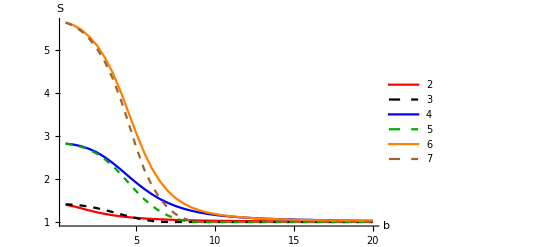

```mathematica
nisingsvet=Show[s2,s3,s4,s5,s6,s7,PlotRange->All,AxesLabel->{"b","S"},LabelStyle->Directive[15, Black,FontFamily->"Times New Roman"]]
```

```mathematica
Export[SystemDialogInput["FileSave", "n234567_ising_svet.png"],nisingsvet,Background->None];
```